```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\reimplementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
pnData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,pnData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractPnData[ds_,directive_,keys_,which_:{1}]:=Module[
{data,x,y,result},
data=Apply[ds,directive];
x=Table[i,{i,0,-1+((data[Take,keys[[1]]]//Normal)[[1]]//Length)}];
y=(data[Take,keys[[2]]]//Normal)[[1]];
result={};
If[Depth[y]==2,result={Table[{x[[it]],y[[it]]},{it,Length[x]}]},
Do[(
pn=y[[i]];
AppendTo[result,Table[{x[[it]],pn[[it]]},{it,Length[x]}]];
),{i,which}]];
Return[result]
]
```

```mathematica
getPlot[data_,k_:0]:=(
SetOptions[LinTicks,TickLengthScale->2.5];

(*colors={Blue,Red};
pltStyle=Table[Directive[color,Opacity[0.7],Dashed],{color,colors}];*)

plt=ListPlot[data,
PlotRange->{Full,{0,0.5}},ImageSize->240,
Frame->True,Axes->False,
FrameStyle->Directive[Black,14,FontFamily->"Bookman Old Style"],
PlotMarkers->{"●", 6},
Joined->True,
Epilog->Text[
Style[StringJoin["p/π = ",ToString[NumberForm[N[2k/pnAvail["size"][[1]]],{2,1}]],"\n λ = ",ToString[NumberForm[B,{2,1}]]],Black,15,FontFamily->"Bookman Old Style"],
{12.5,0.4}],
FrameLabel->{Style["n",Black,14,FontFamily->"Bookman Old Style"],Style["P_n",Black,15,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,12],
(*PlotStyle->pltStyle,*)
AspectRatio->.75,
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,16,2,2],StripTickLabels[LinTicks[0,16,2,2]]}}
];

Show[plt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsPn[which_:{1}]:=Module[
{plots,directive,keys,pn},
directive={Select[#coupling==J&&#interaction==B&]};

plots={};
Do[(
Do[(
p0n=extractPnData[pnDataset,directive,{"momentum","P0n"}];
p1n=extractPnData[pnDataset,directive,{"momentum","P1n"},which];
pn=Table[Table[{p1n[[ii,jj,1]]-p0n[[1,jj,1]],p1n[[ii,jj,2]]},{jj,pnAvail["size"][[1]]+1}],{ii,Length[p1n]}];
Do[
AppendTo[plots,getPlot[pn[[j]],which[[j]]-1]];
,{j,Length[which]}];
),{B,pnAvail["interaction"]//Normal}];
),{J,pnAvail["coupling"]//Normal}];

Return[plots]
];
```

```mathematica
SavePlots[plots_,offset_]:=(
For[it=1,it≤Length[plots],it++,(
filename=StringJoin["../implementation/plots/pn/pn_",StringPadLeft[ToString[offset+it],4,"0"],".png"];
Export[filename,plots[[it]]];
)];
)
```

J ∈ {0.4} @ 16-2-16_0.0-1.0-1.0

Part::partd: Part specification Dataset⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of Dataset⟦1⟧ does not exist.

Part::partw: Part 4 of Dataset⟦1⟧ does not exist.

Part::partw: Part 5 of Dataset⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Dataset⟦1⟧ is longer than depth of object.

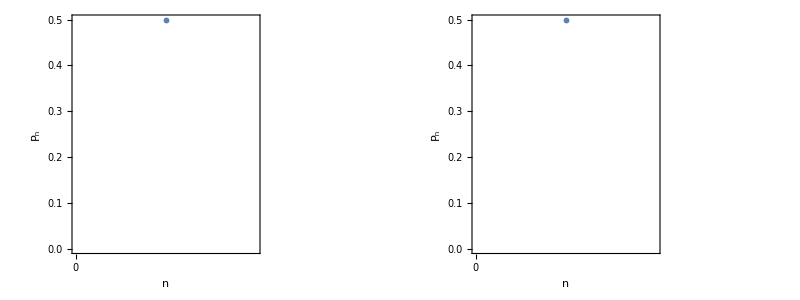

```mathematica
JRange={"0.4"};
tails={"16-2-16_0.0-1.0-1.0"};
pnPlots={};
Do[(
pnDataset=Dataset[getAssoc["pn",JRange,tail]];
pnAvail=Dataset[getStruct[pnDataset]];
Print[Style[StringJoin["J ∈ ",ToString[JRange]," @ ", tail],16]];
AppendTo[pnPlots,makePlotsPn[{1,5,9}]];
Print[Grid[pnPlots]];
),{tail,tails}]
```

```mathematica
(*SavePlots[]*)
```

```mathematica
SavePlots[pnPlots[[1]],0]
```

```mathematica
directive={Select[#coupling==0.4&&#interaction==1&]}
```

{Select[#coupling==0.4&&#interaction==1&]}

```mathematica
pn=extractPnData[pnDataset,directive,{"momentum","P1n"},{1,5,9}]
```

{{{0,0.0125937},{1,0.0219322},{2,0.0465605},{3,0.0609823},{4,0.0787279},{5,0.0874222},{6,0.094608},{7,0.0971732},{8,0.0971732},{9,0.094608},{10,0.0874222},{11,0.0787279},{12,0.0609823},{13,0.0465605},{14,0.0219322},{15,0.0125937},{16,0.}},{{0,0.00967829},{1,0.0176118},{2,0.037803},{3,0.0539698},{4,0.0754098},{5,0.0909792},{6,0.104141},{7,0.110407},{8,0.110407},{9,0.104141},{10,0.0909792},{11,0.0754098},{12,0.0539698},{13,0.037803},{14,0.0176118},{15,0.00967829},{16,0.}},{{0,0.0125937},{1,0.0219322},{2,0.0465605},{3,0.0609823},{4,0.0787279},{5,0.0874222},{6,0.094608},{7,0.0971732},{8,0.0971732},{9,0.094608},{10,0.0874222},{11,0.0787279},{12,0.0609823},{13,0.0465605},{14,0.0219322},{15,0.0125937},{16,0.}}}

```mathematica
pnAvail["size"][[1]]+1
```

17